```mathematica
(*05/16/21*)
(*velocity u_z (constant) inside the norhern Alfven wing generated by a box-like ionospheric obstacle*)
B0= 5.1369 * 10^-9;(*upstream magnetic field in Tesla*)
n0=0.11 * 10^6;(*upstream number density in 1/m^3*)
mp=1.6726231*10^-27; (*proton mass*)
m=7.5 * mp; (*upstream ion mass*)
mu0= 4 * 3.14159265359* 10^-7; (*magnetic permeability of vacuum*)
vA=B0/(√(mu0 * n0 * m)); (*Alfven velocity*)
u0=43*10^3; (*magnitude of upstream flow velocity in m/s*)
MA=u0/vA(*Alfvenic Mach number, Europa*)


uz[theta_,a_]= (B0*Cos[theta])/(√(mu0* n0*m)(1+MA^2+2MA Sin[theta]))*(√(1+MA^2+2MA Sin[theta]-MA^2a^2(1-Sin[theta]*Sin[theta]))+MA*(a-2)*Sin[theta]+MA^2(a-1)-1);
ux[theta_,a_]=u0-B0/(√(mu0* n0*m)(1+MA^2+2MA Sin[theta]))*((Sin[theta]+MA)*√(1+MA^2+2MA Sin[theta]-MA^2a^2(1-Sin[theta]*Sin[theta]))-MA* a*Cos[theta]*Cos[theta]-Sin[theta]*(1+MA^2+2MA Sin[theta]));
```

0.348577

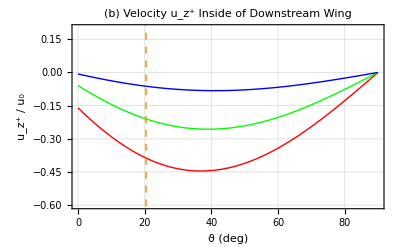

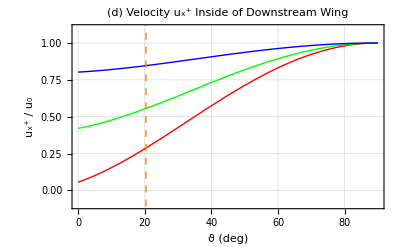

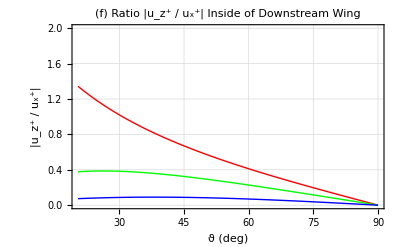

```mathematica
Plot1=Plot[{uz[theta*(2π)/360,0.0]/(u0),uz[theta*(2π)/360,0.4]/(u0),uz[theta*(2π)/360,0.8]/(u0)},{theta, 0, 90}, FrameLabel->{"ϑ (deg)","u_z^+ / u_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(b) Velocity u_z^+ Inside of Downstream Wing", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}}, (*PlotLegends ->{"λ = 1.0","λ = 0.6","λ = 0.2"},*) PlotRange->{-0.6,0.2},Epilog->{Directive[Dashed, Orange],InfiniteLine[{{ArcSin[MA]*360/(2π),-0.6},{ArcSin[MA]*360/(2π),0.2}}]}] 
Plot2=Plot[{ux[theta*(2π)/360,0.0]/(u0),ux[theta*(2π)/360,0.4]/(u0),ux[theta*(2π)/360,0.8]/(u0)},{theta, 0, 90}, FrameLabel->{"ϑ (deg)","u_x^+ / u_0"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(d) Velocity u_x^+ Inside of Downstream Wing", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}}, (*PlotLegends ->{"λ = 1.0","λ = 0.6","λ = 0.2"},*) PlotRange->{-0.1,1.1},Epilog->{Directive[Dashed, Orange],InfiniteLine[{{ArcSin[MA]*360/(2π),-0.1},{ArcSin[MA]*360/(2π),1.1}}]}] 
Plot3=Plot[{Abs[uz[theta*(2π)/360,0.0]/ux[theta*(2π)/360,0.0]],Abs[uz[theta*(2π)/360,0.4]/ux[theta*(2π)/360,0.4]],Abs[uz[theta*(2π)/360,0.8]/ux[theta*(2π)/360,0.8]]},{theta, ArcSin[MA]*360/(2π), 90}, FrameLabel->{"ϑ (deg)","|u_z^+ / u_x^+|"}, GridLines -> Automatic, Frame -> True, PlotLabel ->"(f) Ratio |u_z^+ / u_x^+| Inside of Downstream Wing", PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick}},  (*PlotLegends ->{"λ = 1.0","λ = 0.6","λ = 0.2"},*)PlotRange->{0,2}]
```

```mathematica
Export["figure3b_newNOLEGEND.pdf",Plot1]
Export["figure3d_newNOLEGEND.pdf",Plot2]
Export["figure3f_newNOLEGEND.pdf",Plot3]
```

figure3b_newNOLEGEND.pdf

figure3d_newNOLEGEND.pdf

figure3f_newNOLEGEND.pdf

```mathematica
"figure3_uz_angleV3SOUTHlamS.pdf"
```